MAT120    Assignment 4
Question 5
5. a)
In xy plane:

```mathematica
a1=ContourPlot[{x y==1,x y==2, x y^2==1, x y^2==2},{x,-5,5},{y,-5,5},Axes->True, AxesLabel->Automatic,PlotLegends->"Expressions"];
b1=RegionPlot[ImplicitRegion[1≤ x y ≤ 2 && 1≤ x y^2 ≤ 2 ,{x,y}]];
Show[a1,b1]
```

-Graphics-

```mathematica
Solve[{u==x y, v==x y^2},{x,y}]
```

{{x→u^2/v,y→v/u}}

In uv plane:

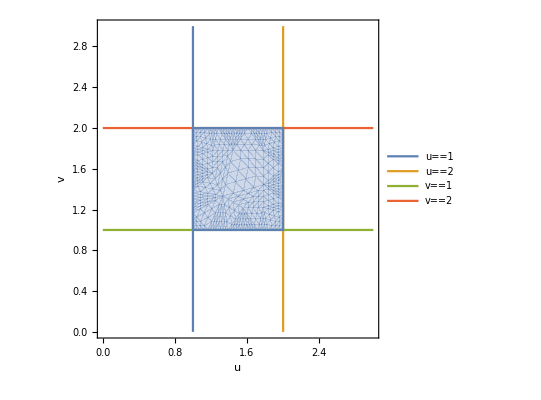

```mathematica
x=u^2/v;
y=v/u;
a2=ContourPlot[{x y==1,x y==2, x y^2==1, x y^2==2},{u,0,3},{v,0,3},Axes->True, AxesLabel->Automatic,PlotLegends->"Expressions"];
b2=RegionPlot[ImplicitRegion[1≤ x y ≤ 2 && 1≤ x y^2 ≤ 2 ,{u,v}]];
Show[a2,b2]
```

5. b)

```mathematica
jac=Det[D[{x,y},{{u,v}}]]
```

1/v

5. c)

```mathematica
∫_1^2 ∫_1^2 y^2(jac)ⅆuⅆv
```

3/4